```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-FA/SMS-stop-FA_CT2",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
```

## Top Self Energy

### Remove diagrams which are identically zero due to color conservation

in total: 2 Particles insertions

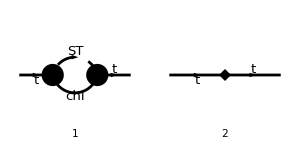

FeynArtsGraphics({t}→{t})(([1] | [2]))

```mathematica
tops = CreateTopologies[1, 1->1,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
topsCT = CreateCTTopologies[1,1->1];
processTT =  { F[9]} -> {F[9]};
allDiags = InsertFields[Join[tops,topsCT],processTT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2],S[3]}];
goodDiags = allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 300,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True]
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
```

in total: 2 Particles amplitudes

-((-ⅈ yDM (γ̄)^7 δ_Col1Col2).(mChi+γ·q).(-ⅈ yDM (γ̄)^6))/((q^2-mChi^2).((q-p)^2-mST^2))+(ⅈ π^2 deltaS yDM^2 δ_Col1Col2 (-(γ·p)).(γ̄)^7)/MT+ⅈ π^2 deltaSp yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6+ⅈ π^2 deltaS yDM^2 δ_Col1Col2

```mathematica
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

(yDM^2 δ_Col1Col2 ((MT (γ·q).(γ̄)^6)/((q^2-mChi^2).((p-q)^2-mST^2))+ⅈ π^2 (deltaS (MT-(γ·p).(γ̄)^7)+deltaSp MT (γ·p).(γ̄)^6)))/MT

```mathematica
ampC = TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify
```

(ⅈ π^2 yDM^2 δ_Col1Col2 (MT (γ·p).(γ̄)^6 (deltaSp-B_1(p^2,mChi^2,mST^2))+deltaS (MT-(γ·p).(γ̄)^7)))/MT

```mathematica
Expand[ampC]
```

-ⅈ π^2 yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6 B_1(p^2,mChi^2,mST^2)-(ⅈ π^2 deltaS yDM^2 δ_Col1Col2 (γ·p).(γ̄)^7)/MT+ⅈ π^2 deltaSp yDM^2 δ_Col1Col2 (γ·p).(γ̄)^6+ⅈ π^2 deltaS yDM^2 δ_Col1Col2

## Renormalization Conditions

```mathematica
fL=Coefficient[Expand[ampC],DiracGamma[Momentum[p,D],D].DiracGamma[7]]
fR=Coefficient[Expand[ampC],DiracGamma[Momentum[p,D],D].DiracGamma[6]]
fSL=Select[Expand[ampC],FreeQ[#,DiracGamma,Infinity]&] (* Since the term without gamma equals PL+PR *)
fSR=Select[Expand[ampC],FreeQ[#,DiracGamma,Infinity]&](* Since the term without gamma equals PL+PR *)
```

-(ⅈ π^2 deltaS yDM^2 δ_Col1Col2)/MT

ⅈ π^2 deltaSp yDM^2 δ_Col1Col2-ⅈ π^2 yDM^2 δ_Col1Col2 B_1(p^2,mChi^2,mST^2)

ⅈ π^2 deltaS yDM^2 δ_Col1Col2

ⅈ π^2 deltaS yDM^2 δ_Col1Col2

```mathematica
MT fL + fSR
```

0

```mathematica
deltaSPsol=deltaSp/.Solve[((MT fR + fSL)/.{Pair[Momentum[p,D],Momentum[p,D]]->MT^2})==0,deltaSp][[1]]
```

(MT B_1(MT^2,mChi^2,mST^2)-deltaS)/MT

```mathematica
lA=1+xC^2+xT^2-2*xC-2*xT-2*xT*xC;
xC = mChi^2/mST^2;
xT=MT^2/mST^2;
lB=-lA;
deltaS1=(-mST/(32*Pi^4*xT^(3/2)))*(xT*(2*xC+xT-2)+(-xC^2+2*xC+xT-1)*Log[xC]-2*(-xC^3+(3+xT)*xC^2+(xT-3)*xC+(xT-1)^2)*Log[(xC-xT+Sqrt[lA]+1)/(2*Sqrt[xC])]/(Sqrt[lA]));
deltaSP1=(1/(64*Pi^4*xT^2))*(2*xT*(xC-xT-1)+(-xC^2+2*xC+xT^2-1)*Log[xC]+2*(xC^3-(3+xT)*xC^2+(xT^2+3)*xC-(xT+1)*(xT-1)^2)*Log[(xC-xT+Sqrt[lA]+1)/(2*Sqrt[xC])]/(Sqrt[lA]));
deltaS2=(-mST/(32*Pi^4*xT^(3/2)))*(xT*(xC-1)+xT*(xC+xT-1)-Sqrt[lB]*(xC-1)*ArcTan[Sqrt[lB]/(1+xC-xT)]+(xC+xT-1)*(xC^2-(2+xT)*xC-xT+1)*ArcTan[Sqrt[lB]/(1+xC-xT)]/Sqrt[lB]-(xC^2-2*xC-xT+1)*Log[xC]);
deltaSp2=(2/(64*Pi^4*xT^2))*(-2*xT^2+xT*(xC+xT-1)+Sqrt[lB]*xT*ArcTan[Sqrt[lB]/(1+xC-xT)]+(xC+xT-1)*(xC^2-(xT+2)*xC-xT+1)*ArcTan[Sqrt[lB]/(1+xC-xT)]/Sqrt[lB]-(xC^2-2*xC-xT^2+1)*Log[xC]/2);
```

```mathematica
deltaSP1
```

(mST^4 ((2 MT^2 (mChi^2/mST^2-MT^2/mST^2-1))/mST^2+(-mChi^4/mST^4+(2 mChi^2)/mST^2+MT^4/mST^4-1) log(mChi^2/mST^2)+(2 (mChi^6/mST^6-(mChi^4 (MT^2/mST^2+3))/mST^4+(mChi^2 (MT^4/mST^4+3))/mST^2-(MT^2/mST^2-1)^2 (MT^2/mST^2+1)) log((mChi^2/mST^2+√(mChi^4/mST^4-(2 mChi^2 MT^2)/mST^4-(2 mChi^2)/mST^2+MT^4/mST^4-(2 MT^2)/mST^2+1)-MT^2/mST^2+1)/(2 √(mChi^2/mST^2))))/(√(mChi^4/mST^4-(2 mChi^2 MT^2)/mST^4-(2 mChi^2)/mST^2+MT^4/mST^4-(2 MT^2)/mST^2+1))))/(64 π^4 MT^4)

```mathematica
deltaSPsol1=Simplify[PaXEvaluate[(deltaSPsol/.{deltaS->deltaS1}),PaXImplicitPrefactor->1/(2 Pi)^(4)]/.{1/Epsilon->0,ScaleMu->mST},Assumptions->{MT>0,mST>0,mChi>0,mST>mChi+MT}]
```

(MT (mChi^4-2 mChi^2 (mST^2+MT^2)+(mST^2-MT^2)^2) ((8 π^4-1) mChi^4+2 (1-8 π^4) mChi^2 mST^2+(mST^2-MT^2) ((8 π^4-1) mST^2-8 π^4 MT^2)) log(mChi^2/mST^2)+MT^3 (mChi^4-2 mChi^2 (mST^2+MT^2)+(mST^2-MT^2)^2) ((2-16 π^4) mChi^2+2 (8 π^4-1) mST^2+MT^2 (1+16 π^4 (-2+ℽ+log(π))))-2 MT √(mChi^4-2 mChi^2 (mST^2+MT^2)+(mST^2-MT^2)^2) ((8 π^4-1) mChi^6-(8 π^4-1) mChi^4 (3 mST^2+MT^2)+mChi^2 (3 (8 π^4-1) mST^4+(1-16 π^4) mST^2 MT^2-8 π^4 MT^4)-(mST^2-MT^2)^2 ((8 π^4-1) mST^2-8 π^4 MT^2)) log((mChi^2+√(mChi^4-2 mChi^2 (mST^2+MT^2)+(mST^2-MT^2)^2)+mST^2-MT^2)/(2 mChi mST)))/(512 π^8 MT^5 (mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))

```mathematica
FullSimplify[deltaSP1-deltaSPsol1,Assumptions->{MT>0,mST>0,mChi>0,mST>mChi+MT}]
```

-1/(512 π^8 MT^4)(MT^2 ((2-32 π^4) mChi^2+(32 π^4-2) mST^2+MT^2 (1+16 π^4 (-1+ℽ+log(π))))+2 (16 π^4-1) ((mChi^2-mST^2)^2-mST^2 MT^2) log(mChi/mST)+(2 (16 π^4-1) ((mChi^2-mST^2)^3-MT^2 (mChi^4+mChi^2 mST^2-2 mST^4)-mST^2 MT^4) log((2 mChi mST)/(mChi^2+√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+mST^2-MT^2)))/(√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))))